# Optical Bloch equations with phenomenological decoherence

```mathematica
M=({{-Γ(1+ϵ), -I Ω/2, I Ω/2, 0}, {-I Ω/2, -Γ(1+2ϵ)/2, 0, I Ω/2}, {I Ω/2, 0, -Γ(1+2ϵ)/2, -I Ω/2}, {Γ, I Ω/2, -I Ω/2, -ϵ Γ}});
asm={Γ>0,ϵ>0,Ω>0,t>0,tp>0};
Q=MatrixExp[M t];
Q0=MatrixExp[M tp]/.{Ω->0};
```

```mathematica
par={Γ->1/(21.42*^-6),ϵ->0,Ω->2Pi 520*^3,tp->5*^-6};
QQ=(Q0.Q.({{0}, {0}, {0}, {1}})//.par)[[4,1]];
```

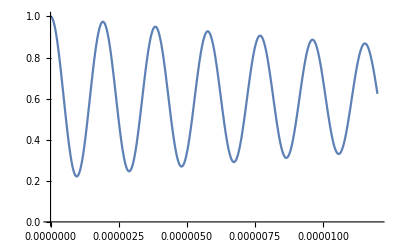

```mathematica
Plot[QQ,{t,0,12*^-6},PlotRange->{All,{0,1}}]
```

```mathematica
Pg=(Q0.Q.({{0}, {0}, {0}, {1}}))[[4,1]];
```

```mathematica
Pavg=(Integrate[Pg,{tp,0,T}]/T)/.{T->tp};
```

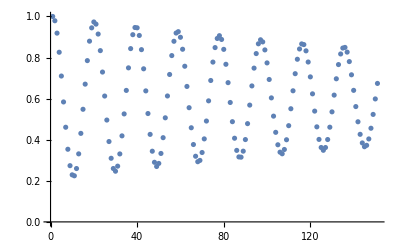

```mathematica
qq=Table[Pg/.par,{t,0,15*^-6,.1*^-6}];
ListPlot[qq,PlotRange->{All,All}]
```

```mathematica
Pavg
```

(ⅇ^(-1/4 t (Γ (3+4 ϵ)+√(Γ^2-16 Ω^2))) ((ⅇ^(1/4 t (3 Γ+√(Γ^2-16 Ω^2))) (Γ^4-14 Γ^2 Ω^2-32 Ω^4))/ϵ+1/(√(Γ^2)-Γ (3+4 ϵ))2 (Γ+2 √(Γ^2)) Ω^2 ((1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))-2 ⅇ^(1/4 t (3 Γ+√(Γ^2-16 Ω^2)))) Γ^2-16 (1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))-2 ⅇ^(1/4 t (3 Γ+√(Γ^2-16 Ω^2)))) Ω^2+3 (-1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))) Γ √(Γ^2-16 Ω^2))+1/(√(Γ^2)+Γ (3+4 ϵ))2 (-Γ+2 √(Γ^2)) Ω^2 ((1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))-2 ⅇ^(1/4 t (3 Γ+√(Γ^2-16 Ω^2)))) Γ^2-16 (1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))-2 ⅇ^(1/4 t (3 Γ+√(Γ^2-16 Ω^2)))) Ω^2+3 (-1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))) Γ √(Γ^2-16 Ω^2))+ⅇ^(-1/4 tp (√(Γ^2)+Γ (3+4 ϵ))) ((ⅇ^(1/4 (tp (3 Γ+√(Γ^2))+t (3 Γ+√(Γ^2-16 Ω^2)))) (-Γ^4+14 Γ^2 Ω^2+32 Ω^4))/ϵ-1/(√(Γ^2)-Γ (3+4 ϵ))2 ⅇ^((tp √(Γ^2))/2) (Γ+2 √(Γ^2)) Ω^2 ((1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))-2 ⅇ^(1/4 t (3 Γ+√(Γ^2-16 Ω^2)))) Γ^2-16 (1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))-2 ⅇ^(1/4 t (3 Γ+√(Γ^2-16 Ω^2)))) Ω^2+3 (-1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))) Γ √(Γ^2-16 Ω^2))-1/(√(Γ^2)+Γ (3+4 ϵ))2 (-Γ+2 √(Γ^2)) Ω^2 ((1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))-2 ⅇ^(1/4 t (3 Γ+√(Γ^2-16 Ω^2)))) Γ^2-16 (1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))-2 ⅇ^(1/4 t (3 Γ+√(Γ^2-16 Ω^2)))) Ω^2+3 (-1+ⅇ^(1/2 t √(Γ^2-16 Ω^2))) Γ √(Γ^2-16 Ω^2)))))/(tp (Γ^5-14 Γ^3 Ω^2-32 Γ Ω^4))